## Illustrate PI control of a nonlinear system (Problem 11.5)

```mathematica
Clear["Global`*"];
```

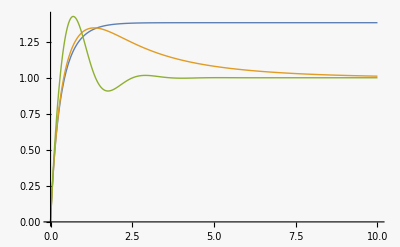

```mathematica
tend=10;
eqs={y'[t]==a y[t]^2+kp(r- y[t])+ ki v[t], v'[t]==  r-y[t]};
init={y[0]==0,v[0]==0};

values0={a->1,kp->5,ki->0} (* parameter values & PI gains *);
sol0=NDSolveValue[{eqs,init}/.values0/.r->1,{y,u},{t,0,tend}];
y0=sol0[[1]];

values1={a->1,kp->5,ki->1} (* parameter values & PI gains *);
sol1=NDSolveValue[{eqs,init}/.values1/.r->1,{y,u},{t,0,tend}];
y1=sol1[[1]];

values2={a->1,kp->5,ki->10} (* parameter values & PI gains *);
sol2=NDSolveValue[{eqs,init}/.values2/.r->1,{y,u},{t,0,tend}];
y2=sol2[[1]];

Plot[{y0[t],y1[t],y2[t]},{t,0,tend},PlotRange->All]
```

Export data

```mathematica
dt=0.01;
y0t=Table[y0[t],{t,0,tend,dt}];
y1t=Table[y1[t],{t,0,tend,dt}];
y2t=Table[y2[t],{t,0,tend,dt}];
(*
SetDirectory[NotebookDirectory[]];Export["nonlinearPI.dat",Flatten/@Transpose[{y0t,y1t,y2t}],"Table"];
*)
```